```mathematica
gsq1[str_String,page_]:=Block[{url},url="https://scholar.google.co.uk/scholar?start="<>URLEncode[page]<>"&q="<>URLEncode[str]<>"&hl=en&as_sdt=0,5";
Cases[Cases[Import[url,"XMLObject"],XMLElement["div",{"id"->"gs_ccl","role"->"main"},___],Infinity],XMLElement["h3",{"class"->"gs_rt"},___],Infinity]]
dataSteg=Table[gsq1["steganography",0i],{i,1,10}];
```

{Information hiding techniques  ,Exploring ,Reliable detection  LSB ,  limits  ,Digital watermarking  ,Hide  seek:  introduction  , information-theoretic model  ,Wherefore art thou r3579x?: anonymized social networks, hidden patterns,  structural ,Digital image ,Spread spectrum image }

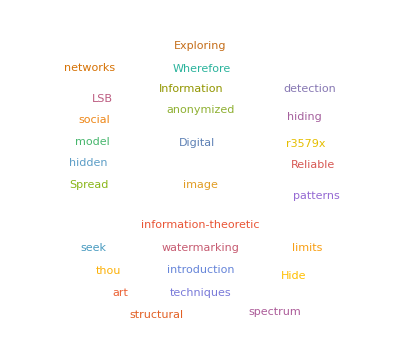

```mathematica
dataSteg;
goodSteg=Table[Cases[dataSteg[[2]][[i]],XMLElement["a",_,_],Infinity][[1]][[3]][[1]],{i,1,10}];
DeleteStopwords@Flatten@TextWords@Table[Cases[dataSteg[[2]][[i]],XMLElement["a",_,_],Infinity][[1]][[3]][[1]],{i,1,10}];
WordCloud@DeleteStopwords@Flatten@TextWords@goodSteg
```

```mathematica
gsq1[str_String,page_]:=Block[{url},url="https://scholar.google.co.uk/scholar?start="<>URLEncode[page]<>"&q="<>URLEncode[str]<>"&hl=en&as_sdt=0,5";
Cases[Cases[Import[url,"XMLObject"],XMLElement["div",{"id"->"gs_ccl","role"->"main"},___],Infinity],XMLElement["h3",{"class"->"gs_rt"},___],Infinity]]

dataSteg=Table[gsq1["steganography",0i],{i,1,10}];

WordCloud@DeleteStopwords@Flatten@TextWords@Table[Cases[dataSteg[[2]][[i]],XMLElement["a",_,_],Infinity][[1]][[3]][[1]],{i,1,10}]
```

-Graphics-

```mathematica
gsq1[str_String,page_]:=Block[{url},url="https://scholar.google.co.uk/scholar?start="<>URLEncode[page]<>"&q="<>URLEncode[str]<>"&hl=en&as_sdt=0,5";
Cases[Cases[Import[url,"XMLObject"],XMLElement["div",{"id"->"gs_ccl","role"->"main"},___],Infinity],XMLElement["h3",{"class"->"gs_rt"},___],Infinity]]

dataSteg=Table[gsq1["steganography",0i],{i,1,20}];
```

```mathematica
dataGet[str_String,page_]:=Table[Block[{url},url="https://scholar.google.co.uk/scholar?start="<>URLEncode[0i]<>"&q="<>URLEncode[str]<>"&hl=en&as_sdt=0,5";
Cases[Cases[Import[url,"XMLObject"],XMLElement["div",{"id"->"gs_ccl","role"->"main"},___],Infinity],XMLElement["h3",{"class"->"gs_rt"},___],Infinity]],{i,1,page}]
parseData[dataIn_]:=DeleteStopwords@Flatten@TextWords@Table[Cases[dataIn,XMLElement["a",_,_],Infinity][[i]][[3]][[1]],{i,1,Length@dataRaw[[1]]*Length@dataRaw}]
```

```mathematica
dataRaw=dataGet["Steganography",10];
```

```mathematica
Length@dataRaw[[1]]*Length@dataRaw
```

100

```mathematica
dataParsed=parseData[dataRaw]
WordCloud@dataParsed
```

{Information,hiding,techniques,Exploring,Reliable,detection,LSB,limits,Digital,watermarking,Hide,seek,introduction,information-theoretic,model,Wherefore,art,thou,r3579x,anonymized,social,networks,hidden,patterns,structural,Digital,image,Spread,spectrum,image,Information,hiding,techniques,Exploring,Reliable,detection,LSB,limits,Digital,watermarking,Hide,seek,introduction,information-theoretic,model,Wherefore,art,thou,r3579x,anonymized,social,networks,hidden,patterns,structural,Digital,image,Spread,spectrum,image,Information,hiding,techniques,Exploring,Reliable,detection,LSB,limits,Digital,watermarking,Hide,seek,introduction,information-theoretic,model,Wherefore,art,thou,r3579x,anonymized,social,networks,hidden,patterns,structural,Digital,image,Spread,spectrum,image,Information,hiding,techniques,Exploring,Reliable,detection,LSB,limits,Digital,watermarking,Hide,seek,introduction,information-theoretic,model,Wherefore,art,thou,r3579x,anonymized,social,networks,hidden,patterns,structural,Digital,image,Spread,spectrum,image,Information,hiding,techniques,Exploring,Reliable,detection,LSB,limits,Digital,watermarking,Hide,seek,introduction,information-theoretic,model,Wherefore,art,thou,r3579x,anonymized,social,networks,hidden,patterns,structural,Digital,image,Spread,spectrum,image,Information,hiding,techniques,Exploring,Reliable,detection,LSB,limits,Digital,watermarking,Hide,seek,introduction,information-theoretic,model,Wherefore,art,thou,r3579x,anonymized,social,networks,hidden,patterns,structural,Digital,image,Spread,spectrum,image,Information,hiding,techniques,Exploring,Reliable,detection,LSB,limits,Digital,watermarking,Hide,seek,introduction,information-theoretic,model,Wherefore,art,thou,r3579x,anonymized,social,networks,hidden,patterns,structural,Digital,image,Spread,spectrum,image,Information,hiding,techniques,Exploring,Reliable,detection,LSB,limits,Digital,watermarking,Hide,seek,introduction,information-theoretic,model,Wherefore,art,thou,r3579x,anonymized,social,networks,hidden,patterns,structural,Digital,image,Spread,spectrum,image,Information,hiding,techniques,Exploring,Reliable,detection,LSB,limits,Digital,watermarking,Hide,seek,introduction,information-theoretic,model,Wherefore,art,thou,r3579x,anonymized,social,networks,hidden,patterns,structural,Digital,image,Spread,spectrum,image,Information,hiding,techniques,Exploring,Reliable,detection,LSB,limits,Digital,watermarking,Hide,seek,introduction,information-theoretic,model,Wherefore,art,thou,r3579x,anonymized,social,networks,hidden,patterns,structural,Digital,image,Spread,spectrum,image}

-Graphics-

```mathematica
Table[Cases[dataSteg[[2]][[i]],XMLElement["a",_,_],Infinity][[1]][[3]][[1]],{i,1,10}]
```

{Information hiding techniques for ,Exploring ,Reliable detection of LSB ,On the limits of ,Digital watermarking and ,Hide and seek: An introduction to ,An information-theoretic model for ,Wherefore art thou r3579x?: anonymized social networks, hidden patterns, and structural ,Digital image ,Spread spectrum image }

```mathematica
[[1]][[3]][[1]]
```

```mathematica
WordCloud@DeleteStopwords@Flatten@TextWords@Table[Cases[dataSteg,XMLElement["a",_,_],Infinity][[i]][[3]][[1]],{i,1,20}]
```

-Graphics-

```mathematica
cloud[str_String,page_]:=gsq1[Block[{url},url="https://scholar.google.co.uk/scholar?start="<>URLEncode[page]<>"&q="<>URLEncode[str]<>"&hl=en&as_sdt=0,5";
Cases[Cases[Import[url,"XMLObject"],XMLElement["div",{"id"->"gs_ccl","role"->"main"},___],Infinity],XMLElement["h3",{"class"->"gs_rt"},___],Infinity]]]
```

```mathematica
cloud["steganography",5]
```

gsq1[{XMLElement[h3,{class→gs_rt},{XMLElement[a,{shape→rect,href→http://ieeexplore.ieee.org/xpls/abs_all.jsp?arnumber=1203220,data-clk→hl=en&sa=T&ct=res&cd=5&ei=AdMAWMLaJ4GzmAGGkaKYDg&scisig=AAGBfm1KpWp98zCKfse2fWBWcFHn0tfPtg&nossl=1},{Hide and seek: An introduction to ,XMLElement[b,{},{steganography}]}]}],XMLElement[h3,{class→gs_rt},{XMLElement[a,{shape→rect,href→http://link.springer.com/chapter/10.1007/3-540-49380-8_21,data-clk→hl=en&sa=T&ct=res&cd=6&ei=AdMAWMLaJ4GzmAGGkaKYDg&scisig=AAGBfm3Ft3iCbq99Ec_ZTMPFjGYXTMIX7A&nossl=1},{An information-theoretic model for ,XMLElement[b,{},{steganography}]}]}],XMLElement[h3,{class→gs_rt},{XMLElement[a,{shape→rect,href→http://dl.acm.org/citation.cfm?id=1242598,data-clk→hl=en&sa=T&ct=res&cd=7&ei=AdMAWMLaJ4GzmAGGkaKYDg&scisig=AAGBfm176rEhBjHHHGWYfZp-Vka-Btngww&nossl=1},{Wherefore art thou r3579x?: anonymized social networks, hidden patterns, and structural ,XMLElement[b,{},{steganography}]}]}],XMLElement[h3,{class→gs_rt},{XMLElement[a,{shape→rect,href→http://www.sciencedirect.com/science/article/pii/S0165168409003648,data-clk→hl=en&sa=T&ct=res&cd=8&ei=AdMAWMLaJ4GzmAGGkaKYDg&scisig=AAGBfm2tmNApH1V1bqCrkZ4l4jvx-gsH4Q&nossl=1},{Digital image ,XMLElement[b,{},{steganography}],: Survey and analysis of current methods}]}],XMLElement[h3,{class→gs_rt},{XMLElement[a,{shape→rect,href→http://ieeexplore.ieee.org/xpls/abs_all.jsp?arnumber=777088,data-clk→hl=en&sa=T&ct=res&cd=9&ei=AdMAWMLaJ4GzmAGGkaKYDg&scisig=AAGBfm1yssfXxctV3EXSpftqJB1ulZp2Uw&nossl=1},{Spread spectrum image ,XMLElement[b,{},{steganography}]}]}],XMLElement[h3,{class→gs_rt},{XMLElement[a,{shape→rect,href→http://ieeexplore.ieee.org/xpls/abs_all.jsp?arnumber=1206706,data-clk→hl=en&sa=T&ct=res&cd=10&ei=AdMAWMLaJ4GzmAGGkaKYDg&scisig=AAGBfm1s-dBavjld29kjuXdj23g8Mr5BAw&nossl=1},{Detection of LSB ,XMLElement[b,{},{steganography }],via sample pair analysis}]}],XMLElement[h3,{class→gs_rt},{XMLElement[a,{shape→rect,href→http://ieeexplore.ieee.org/xpls/abs_all.jsp?arnumber=958299,data-clk→hl=en&sa=T&ct=res&cd=11&ei=AdMAWMLaJ4GzmAGGkaKYDg&scisig=AAGBfm2ZJsi_rshtyi2---QNFgm_VOnNIQ&nossl=1},{Analysis of LSB based image ,XMLElement[b,{},{steganography }],techniques}]}],XMLElement[h3,{class→gs_rt},{XMLElement[a,{shape→rect,href→http://dl.acm.org/citation.cfm?id=1022597,data-clk→hl=en&sa=T&ct=res&cd=12&ei=AdMAWMLaJ4GzmAGGkaKYDg&scisig=AAGBfm2zbrBfY7fzcAGI6NeOrXQCfFsSmw&nossl=1},{Cyber warfare: ,XMLElement[b,{},{steganography }],vs. steganalysis}]}],XMLElement[h3,{class→gs_rt},{XMLElement[a,{shape→rect,href→http://ieeexplore.ieee.org/xpls/abs_all.jsp?arnumber=935180,data-clk→hl=en&sa=T&ct=res&cd=13&ei=AdMAWMLaJ4GzmAGGkaKYDg&scisig=AAGBfm0WMQcV5u00sSACV62ppjxYkAn-9w&nossl=1},{Digital ,XMLElement[b,{},{steganography}],: hiding data within data}]}],XMLElement[h3,{class→gs_rt},{XMLElement[a,{shape→rect,href→https://www.google.com/patents/US5636292,data-clk→hl=en&sa=T&ct=res&cd=14&ei=AdMAWMLaJ4GzmAGGkaKYDg&scisig=AAGBfm1osN045SMdIQGU-hBrt8mm3ZJJ4w&nossl=1},{XMLElement[b,{},{Steganography }],methods employing embedded calibration data}]}]}]

```mathematica
URLEncode[02]
```

2

```mathematica
dataGet[str_String,page_]:=Table[Block[{url},url="https://scholar.google.co.uk/scholar?start="<>URLEncode[0i]<>"&q="<>URLEncode[str]<>"&hl=en&as_sdt=0,5";
Cases[Cases[Import[url,"XMLObject"],XMLElement["div",{"id"->"gs_ccl","role"->"main"},___],Infinity],XMLElement["h3",{"class"->"gs_rt"},___],Infinity]],{i,1,page}]
t1dataGet[str_String]:=Table[Block[{url},url="https://scholar.google.co.uk/scholar?start="<>URLEncode[0i]<>"&q="<>URLEncode[str]<>"&hl=en&as_sdt=0,5";
Cases[Cases[Import[url,"XMLObject"],XMLElement["div",{"id"->"gs_ccl","role"->"main"},___],Infinity],XMLElement["h3",{"class"->"gs_rt"},___],Infinity]],{i,1,1}]
t2dataGet[str_String]:=Table[Block[{url},url="https://scholar.google.co.uk/scholar?start="<>URLEncode[i]<>"&q="<>URLEncode[str]<>"&hl=en&as_sdt=0,5";
Cases[Cases[Import[url,"XMLObject"],XMLElement["div",{"id"->"gs_ccl","role"->"main"},___],Infinity],XMLElement["h3",{"class"->"gs_rt"},___],Infinity]],{i,2,2}]
```